```mathematica
{1920,1080}*.419
```

{804.48,452.52}

```mathematica
FactorInteger[1920]
```

{{2,7},{3,1},{5,1}}

```mathematica
1920/2
```

960

```mathematica
1080/2
```

540

```mathematica
Divisors/@{1920,1080}
```

{{1,2,3,4,5,6,8,10,12,15,16,20,24,30,32,40,48,60,64,80,96,120,128,160,192,240,320,384,480,640,960,1920},{1,2,3,4,5,6,8,9,10,12,15,18,20,24,27,30,36,40,45,54,60,72,90,108,120,135,180,216,270,360,540,1080}}

```mathematica
files=FileNames[__~~"001.png",FileNameJoin[{NotebookDirectory[],"build","frames"}]]
```

{/Users/john/src/tiim.dck/build/frames/00001.png}

```mathematica
frame=Import[files[[1]]]
```

-Graphics-

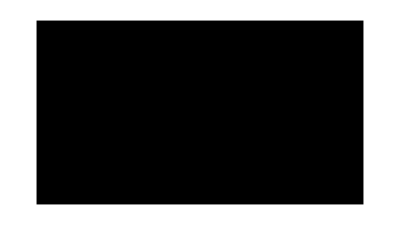

```mathematica
Graphics[{Rectangle[{0,0},{960,540}]}]
```